```mathematica
ex1=Grid[{{
-Graphics-,
Spacer[1],
Style[
(*Column[{ 
Item[ButtonBar[{Graphics[{Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->20]:>FrontEndTokenExecute[InputNotebook[],"SelectionOpenAllGroups"],Graphics[{Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->20]:>FrontEndTokenExecute[InputNotebook[],"SelectionCloseAllGroups"]
},Background->RGBColor[0.811765,0.721569,0.486275]],Alignment->Center],*)
Column[{
ActionMenu[Style[" Contents ",16],{
Style["Ideal Solutions",Bold,15]:>NotebookLocate["Ideal Solutions"],
Framed@Style["Pressure-Composition Diagrams (P-x-y)",Bold,14]:>NotebookLocate["Pressure-Composition Diagrams"],
Style["Raoult's Law",Bold,Italic,13]:>NotebookLocate["Raoult's Law"],
Row[{Style["Screencast:",Bold]," Raoult's Law"}]:>NotebookLocate["link 1"],
"💡 Derivation of Raoult's Law":>NotebookLocate["Derivation of Raoult's Law"],
Style["Mapping a P-x-y Diagram",Bold,Italic,13]:>NotebookLocate["Mapping a P-x-y Diagram"],
Style["Figure 1",Italic]:>NotebookLocate["Figure 1"],
Style["Lever Rule",Bold,Italic,13]:>NotebookLocate["Lever Rule"],
Row[{Style["Screencast:",Bold]," Lever Rule"}]:>NotebookLocate["link 2"],
Style["Figure 2",Italic]:>NotebookLocate["Figure 2"],
"Test Yourself":>NotebookLocate["Concept Test 1"],
"💡 Solution":>NotebookLocate["Solution 1"],
Style["Figure 3",Italic]:>NotebookLocate["Figure 3"],
Style["Changes in Pressure",Bold,Italic,13]:>NotebookLocate["Changes in Pressure"],
"Effect on Liquid and Vapor Amounts (Lever Rule)":>NotebookLocate["Effect on Liquid and Vapor Amounts (Lever Rule)"],
Style["Figure 4",Italic]:>NotebookLocate["Figure 4"],
"Effect on Molar Composition in the Liquid and Vapor Phases":>NotebookLocate["Effect on Molar Composition in the Liquid and Vapor Phases"],
"Test Yourself":>NotebookLocate["Concept Test 2"],
Style["Figure 5",Italic]:>NotebookLocate["Figure 5"],
Style["Figure 6",Italic]:>NotebookLocate["Figure 6"],
Row[{Style["Screencast:",Bold]," Add a Component to Binary system in VLE"}]:>NotebookLocate["link 3"],
"Test Yourself":>NotebookLocate["Concept Test 3"],
Style["Figure 7",Italic]:>NotebookLocate["Figure 7"],
Style["Changes in Temperature",Bold,Italic,13]:>NotebookLocate["Changes in Temperature"],
"Exercise 1":>NotebookLocate["Exercise 1"],
Style["Figure 8",Italic]:>NotebookLocate["Figure 8"],
"Test Yourself":>NotebookLocate["Concept Test 4"],
"💡 Solution":>NotebookLocate["Solution 4"],
Style["Figure 9",Italic]:>NotebookLocate["Figure 9"],
"Test Yourself":>NotebookLocate["Concept Test 5"],
Style["Figure 10",Italic]:>NotebookLocate["Figure 10"],
"Test Yourself":>NotebookLocate["Concept Test 6"],
Style["Figure 11",Italic]:>NotebookLocate["Figure 11"],
Framed@Style["Temperature-Composition Diagrams (T-x-y)",Bold,14]:>NotebookLocate["Temperature-Composition Diagrams"],
Style["Raoult's Law",Bold,Italic,13]:>NotebookLocate["Raoult's Law T-x-y"],
Style["Figure 12",Italic]:>NotebookLocate["Figure 12"],
Row[{Style["Screencast:",Bold]," Bubble Temperature: Raoult's Law"}]:>NotebookLocate["link 4"],
Style["Mapping a T-x-y Diagram",Bold,Italic,13]:>NotebookLocate["Mapping a T-x-y Diagram"],
Style["Figure 13",Italic]:>NotebookLocate["Figure 13"],
Style["Changes in Temperature",Bold,Italic,13]:>NotebookLocate["Changes in Temperature T-x-y"],
"Effect on Liquid and Vapor Amounts (Lever Rule)":>NotebookLocate["Effect on Liquid and Vapor Amounts (Lever Rule) T-x-y"],
Style["Figure 14",Italic]:>NotebookLocate["Figure 14"],
Row[{Style["Screencast:",Bold]," T-x-y Diagram: Lever Rule (Review)"}]:>NotebookLocate["link 5"],
"Effect on Molar Composition in the Liquid and Vapor Phases":>NotebookLocate["Effect on Molar Composition in the Liquid and Vapor Phases T-x-y"],
"Test Yourself":>NotebookLocate["Concept Test 7"],
Style["Figure 15",Italic]:>NotebookLocate["Figure 15"],
Style["Figure 16",Italic]:>NotebookLocate["Figure 16"],
Row[{Style["Screencast:",Bold]," Phase Equilibrium: T-x-y Diagram"}]:>NotebookLocate["link 6"],
"Adding Energy to a System":>NotebookLocate["Adding Energy to a System"],
Style["Figure 17",Italic]:>NotebookLocate["Figure 17"],
Style["Changes in Pressure",Bold,Italic,13]:>NotebookLocate["Changes in Pressure T-x-y"],
"Test Yourself":>NotebookLocate["Concept Test 8"],
Style["Figure 18",Italic]:>NotebookLocate["Figure 18"]
},Background->RGBColor[0.811765,0.721569,0.486275]]
(*},Alignment->Left]*),Text@Style["Baumann,  Falconer,  Nicodemus",White,Bold,13,FontFamily->"Arial"]}],
FontFamily->"Arial"]
}},ItemSize->{{38,20}}];

SetOptions[EvaluationNotebook[],{DockedCells->Cell[BoxData[ToBoxes[ex1]/.{(ImageSize->{___,___})->(ImageSize->{1399,10})}],"DockedCell",Background->Black,ImageMargins->0,CellMargins->{{0,0},{0,0}},CellFrameMargins->{{0,0},{0,0}}]}
];
```

# Vapor-liquid equilibrium (VLE) for ideal solutions

## Objectives

## ### List the 4 or 5 things that want the user to know/understand/be able to do after using this tutorial

## Pressure-composition (P-x-y) diagrams

The Gibbs’ phase rule determines the number of degrees of freedom for a non-reactive system:

F=C-P+2

where F is the number of degrees of freedom, C is the number of components, and P is the number of phases. For a single  component (C = 1) at vapor-liquid equilibrium (P = 2), then F= 1 - 2 + 2 = 1.  If pressure is fixed, the boiling temperature is fixed, so all the liquid boils at the same temperature. For a binary mixture (C = 2) in VLE (P = 2), F = 2 - 2 +2 = 2, so that if the temperature if fixed, the pressure can be changed and still maintain VLE.  When the pressure changes, the compositions of the liquid and vapor also change.

## Raoult’s Law

### When I revised, I did not try to make the correct subscripts nor did I spell check. I used the ### notation to indicate comments

The mole fractions in the liquid and vapor phases that are in equilibirum are given by Raoult's law,

x1P1sat = y1P and x2P2sat = y2P

where xi represents liquid-phase mole fractions and yi represents gas-phase mole fractions, and P is the total pressure. P1sat and P2sat are saturation pressures and can be obtained from Antoine equations:

log_10(P_i^sat)=A-B/(T+C)

### change the Antoine equation so B is the same size as A in font. Also make subscript i’s for A, B, C

where Ai, Bi, Ci are constants for a given component.

The P versus x1 plot is the bubble-point (BP) curve, and corresponds to the pressure (for a fixed temperature) where the first bubble of vapor appears as the pressure decreases.

PBP = yiP +y2P

That is, the sum of the partial pressures is the total pressure. Using Raoult’s law then yields:

P_BP=P_x= x_1 P_1^sat+x_2 P_2^sat =x_1 P_1^sat+(1-x_1) P_2^sat                                                       (1)

### I did not know how to copy the equation with the highlighting. Note that I think should number equations here

which is a straight line.

The P versus  y1 plot is the dew-point (DP) curve, and corresponds to the pressure where the first drop of liquid appears as the pressure increases. These can be calculated for an ideal liquid solution and an ideal gas using Raoult's law:

P_BP=P_x= x_1 P_1^sat+x_2 P_2^sat =x_1 P_1^sat+(1-x_1) P_2^sat                                                       (1)

P_DP=P_y=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)                                                                                                                         (2)

View this screencast that explains Raoult’s law. (Raoult’s Law Explanation).

## make the word screencast a link to the screencast instead of (Raoult’s law explanation)

### ## I removed the heading but apparently there was a way to see the equations but the reader would not know that. What does the symbol on the ledt mean?

To calculate the dew-point (DP), Raolut’s law for each component is substituted ino the equation ∑x_i=1. The temperature and the gas-phase mole fractions are known, but the pressure and the liquid phase mole fractions need to be calculated. This is referred to as a dew-point pressure calculation

####  #Could have hidden the details of these steps.

y_1 P/P_1^sat+y_2 P/P_2^sat  = y_1 P/P_1^sat+(1-y_1) P/P_2^sat=1

This equation can be solved for the dew-point pressure

P=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)

Raolut’s law can then be used to calculate x1 and x2

## Pressure-composition (P-x-y) diagrams

The P-x-y diagram in Figure 1 is at one temperature. The blue line in Figure 1 represents the bubble point; only liquid exists above this line. The green line represents the dew point; below this line, only vapor is present. Liquid and vapor are in equilibrium Inside the shaded region between.

### can you label the blue and green lines instead of using a key? Also, do not put a hyphen between the word bubble and point and between dew and point. Do not put a hyphen betwee 2 and phase and label it 2 phases.

#### the numbers on the x and y axes need to be bigger (and also for other figures so they look the same)

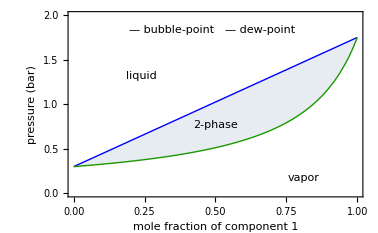
-Graphics-
Figure 1

```mathematica
Framed@Column[{
(*Manipulate[*)Framed@Module[{Px,Py,Psat1,Psat2},
Psat1=1.75;
Psat2=0.3;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0,2.}},Frame->True,Background->White,(*PlotLabel->Style[Row[{Subsuperscript["P","1","sat"]," > "Subsuperscript["P","2","sat"]}],17,FontFamily->"Arial"],*)FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->500,Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->{
Inset[Text@Style["liquid",18,FontFamily->"Arial",Darker[Gray,0.4]],Scaled[{0.25,0.65}]],
Inset[Text@Style["vapor",18,FontFamily->"Arial",Darker[Gray,0.4]],Scaled[{0.8,0.1}]],
Inset[Text@Style["2-phase",18,FontFamily->"Arial",Darker[Gray,0.4]],{0.5,0.5*(Px[0.5]+Py[0.5])}],
Inset[Text@Style[Row[{Style["—",20,Blue]," bubble-point"}],16,FontFamily->"Arial"],Scaled[{0.35,0.9}]],
Inset[Text@Style[Row[{Style["—",20,RGBColor[0.1,0.6,0]]," dew-point"}],16,FontFamily->"Arial"],Scaled[{0.65,0.9}]]
}]],
(*Text@Style["saturation pressures (bar):",FontFamily->"Arial",13],
{{Psat1,1.75,"component 1"},1.65,2.5,0.05},
{{Psat2,0.3,"component 2"},0.1,0.4,0.01}],*)
Text@Style["Figure 1",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center](*,FrameStyle->Lighter[Gray,0.4]]*)
```

## Lever Rule

The relative amounts of liquid and vapor for any point in the two-phase region can be caculated using the lever rule, which is just a mass balance. An derivation of the lever rule is given in the screencast  xxxxxx (need one that uses Pxy diagram). For a basis of one mole total, then L is the liquid amount and V is the vapor amount in the equations below.

### fro this equations, rearrange so postiive numbers (for second equation  f^L = (z1-x1)/(y1-x1)

liquid amount present at z:     L=(y_1-z_1)/(y_1-x_1)

vapor amount present at z:      V=(x_1-z_1)/(x_1-y_1)

Mouseover Figure 2 to see what points are used in the lever rule calculation.

### I tried to make figure 2 smaller but then it does not  work with the mouse and it jumps between sizes when I use the mouse. I think all the figures should be smaller. I did not know how to make bigger. I like shoing the percent on the figure

```mathematica
Framed[Column[{
Framed@Module[{p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
p=0.733;
Psat1=1.569; 
Psat2=0.319; 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.4<y1,(y1-0.4)/(y1-x1),
Px[0.4]≤p,1,
Py[0.4]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,PlotRange->{{0,1},{0.3,1.6}},FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.4,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+0.04},{0.39,p+0.04},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+0.04},{(x1+0.4)/2,p+0.4}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+0.04},{y1,p+0.04},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+0.04},{(0.4+y1)/2,p+0.4}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],17,FontFamily->"Arial"],{(y1+0.4)/2,p+0.5}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],17,FontFamily->"Arial"],{(x1+0.4)/2,p+0.5}]
}];
p3=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+0.04},{0.39,p+0.04},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+0.04},{(x1+0.4)/2,p+0.4}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+0.04},{y1,p+0.04},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+0.04},{(0.4+y1)/2,p+0.4}}]},
Text[Style["L",17,FontFamily->"Arial"],{(y1+0.4)/2,p+0.45}],
Text[Style["V",17,FontFamily->"Arial"],{(x1+0.4)/2,p+0.45}],
{PointSize[0.015],Point[{x1,p}]},Text[Style["x_1",17,FontFamily->"Arial"],{x1,p},{-1,1}],
{PointSize[0.015],Point[{0.4,p}]},Text[Style["z_1",17,FontFamily->"Arial"],{0.415,p},{-1,1}],
{PointSize[0.015],Point[{y1,p}]},Text[Style["y_1",17,FontFamily->"Arial"],{y1,p},{-1,1}]
}];
Mouseover[Show[p1,p2,Background->White],Show[p1,p3,Background->White]]
],
Text@Style["Figure 2",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]]
```

Figure 2

Test Yourself

For the system in Figure 2, use the lever rule to calculate the fraction of liquid and vapor present for an overall molar composition z_1=0.6 and a pressure of 0.x bar.

### I don’s see how a reader will know they can access the solution by clicking on the right

#### Solution

### change so do not use the notation f^L

## for the equations below make the denominator y1-x1 in both cases (so numerator is y1-z1 in the first equation) so that working with positive numbers. Also, need bigger fonts for the equations- the mole fractions in numerator and enominator are too small.

The fraction of liquid  (f^L) is,
 
	f^L=L/(L+V)=(z_1-y_1)/(x_1-y_1)=(0.6-0.71)/(0.33-0.71)=0.29   or  29%   liquid
	
The fraction of vapor  (f^V) is,
 
	f^V=V/(L+V)=(z_1-x_1)/(y_1-x_1)=(0.6-0.33)/(0.71-0.33)=0.71   or  71%  vapor

Use the simulation in Figure 3 to see how the amounts of liquid and vapor change as the overall composition change by moving the slider.

### # in the figure below, label the vapor and liquid regions (not the 2-phase region). Also change notation so the two sides are just labeled V and L

```mathematica
Framed[Column[{Manipulate[
Module[{p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
p=0.733;
Psat1=1.569; 
Psat2=0.319; 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<comp<y1,(y1-comp)/(y1-x1),
Px[comp]≤p,1,
Py[comp]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.,1.75}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{comp,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{comp,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{comp,p},{y1,p}}]},
If[comp>0.33,{Thickness[0.0045],Line[{{x1,p},{x1,p+0.04},{comp-0.01,p+0.04},{comp-0.01,p}}]}],{Thickness[0.0045],Line[{{(x1+comp)/2,p+0.04},{(x1+comp)/2,p+0.4}}]},
If[comp<0.71,{Thickness[0.0045],Line[{{comp+0.01,p},{comp+0.01,p+0.04},{y1,p+0.04},{y1,p}}]}],{Thickness[0.0045],Line[{{(comp+y1)/2,p+0.04},{(comp+y1)/2,p+0.4}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],17,FontFamily->"Arial",Background->White],{(y1+comp)/2,p+0.55}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],17,FontFamily->"Arial"],{(x1+comp)/2,p+0.55}]
}];
p3=Graphics[{
{Thickness[0.003425],Line[{{0.05+(y1+comp)/2,0.4},{(y1+comp)/2,p}}]},
Text[Framed[Style["f^L=L/(L + V)",17,FontFamily->"Arial"],Background->White],{(y1+comp)/2,0.3},{-1,0}],
{Thickness[0.003425],Line[{{-0.05+(x1+comp)/2,0.4},{(x1+comp)/2,p}}]},
Text[Framed[Style["f^V=V/(L + V)",17,FontFamily->"Arial"],Background->White],{(x1+comp)/2,0.3},{1,0}]
}];
Show[p1,p2,p3]],
{{comp,0.6,Style["overall molar composition (z_1)",13,FontFamily->"Arial"]},0.33,0.71,0.01,Appearance->"Labeled"}],
Text@Style["Figure 3",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 3

## Pressure dependence

### ## I removed a heading here and elsewhere. Need tol eliminate the extra line

Move the pressure slider in Figure 4 and observed how the fractions of liquid and vapor change (the bar graph on the right) at a constant overall composition of 0.5. Note how the compositions of both phases change as the presure changes.   Also, I think 2 significant figures for the pressure slider is sufficient.

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.3,1.6}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->{450,300},
Epilog->Inset[Graphics[{PointSize[0.09],Point[{0,0}]}],{0.5,p}]];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{p,0.707,Style["pressure (bar)",13,FontFamily->"Arial"]},0.4,1.25,0.05,Appearance->"Labeled"}],
Text@Style["Figure 4",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 4

### Pressure Effect on Molar Composition

Test Yourself
###How does the user know what the correct answer is? I notice in the printout that it says which answers are incorrect but I don’t see how a reader could select an answer

A piston-cylinder system (Figure 5) contains components A and B in VLE with x_A=0.25 and y_A=0.5. A small weight is added to the piston at constant temperature. What happens as pressure increases?

A. x_A increases, y_A decreases

Incorrect.

B. x_A increases, y_A increases

Correct. Use the slider in Figure 6 to increase the pressure and see what effect it has on x_A and y_A.

B. x_A increases, y_A increases

Correct. Use the slider in Figure 6 to increase the pressure and see x_A and y_A increase.

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x0,y0,x1,y1,leverx,levery,p1,p2},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x0=X/.FindRoot[0.7==X*Psat1+(1-X)*Psat2,{X,0}];
y0=Y/.FindRoot[0.7==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.1,1.6}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->400];

p2=Graphics[{
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,0.7},{0.5,0.7}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{0.5,0.7},{y0,0.7}}]},
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,0.7},{x0,0.1}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{y0,0.7},{y0,0.1}}]},
{Gray,PointSize[0.02],Point[{0.5,0.7}]},

{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]},
{Thick,Dashed,Blue,Line[{{x1,p},{x1,0.133}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{y1,p},{y1,0.133}}]},
{PointSize[0.02],Point[{0.5,p}]},
If[p==0.7,Text@"",{{Thick,Arrow[{{x0,0.2},{x1,0.2}}]},{Thick,Arrow[{{y0,0.2},{y1,0.2}}]}}]
}];
Show[p1,p2]
],{{p,0.7,"pressure (bar)"},0.55,0.9,0.01,Appearance->"Labeled"}],
Text@Style["Figure 6",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 6

C. x_A decreases, y_A decreases

Incorrect.

D. x_A decreases, y_A increases

Incorrect.

```mathematica
Framed@Column[{
Framed@Graphics3D[{
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,2}},0.75]},
{Gray,Cylinder[{{0,0,1.5},{0,0,1.75}},0.75]},
{RGBColor[0.,0.65,0.9],Cylinder[{{0,0,0},{0,0,0.55}},0.75]},
{FaceForm[Black],Cuboid[{-0.25,0,2.25},{0.25,0,2.65}]},
{Thickness[0.02],Arrowheads[0.05],Arrow[{{0,0,2.25},{0,0,1.85}}]},
Text[Style[Column[{"vapor","y_A = 0.5"},Alignment->Center],18,FontFamily->"Arial"],{0,0,1.}],
Text[Style[Column[{"liquid","x_A = 0.25"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},Background->White,ImageSize->150],
Text@Style["Figure 5",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]
```

-Graphics3D-
Figure 5

Screencasts that describe system in more detail: Increase Pressure on Binary VLE System (Interactive) and Pressure Effect on VLE

Test Yourself

### Where is figure 6???

A 50/50 mol% liquid mixture of n-pentane and n-heptane is at 1.2-bar pressure in Figure 7. The pressure is lowered isothermally until the mixture begins to vaporize at about 0.95 bar.  P_P^sat>P_H^sat. Which statements is true?

A. n-Heptane is enriched in the vapor phase

Incorrect.

B. n-Pentane is enriched in the vapor phase

Correct. n-Pentane is the more volatile component so it will be enriched in the vapor phase.

C. The composition in the vapor phase is 50/50 mol%

Incorrect.

D. The mixture does not vaporize

Incorrect.

#### Not sure how incorrect shows up

### In the figure change wording to  select the play button to show what happens when the pressure decreases

```mathematica
Framed[Column[{
Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverL,leverV},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=x/.FindRoot[x*Psat1+(1-x)*Psat2==P,{x,0.4}];
y1=x/.FindRoot[(x/Psat1+(1-x)/Psat2)^-1==P,{x,0.5}];
leverL=If[P<Px[0.5],(0.5-y1)/(x1-y1),1];
leverV=1-leverL;
Show[Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Frame->True,FrameLabel->{Style[Row[{"mole fraction of ",Style["n",Italic],"-pentane"}],17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},PlotRange->{{0,1},{0.1,1.6}},
LabelStyle->FontSize->16,ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.045],Point[{0,0}]}],{0.5,P}]],
If[P<Px[0.5],
Graphics[{
{Thick,Blue,Dashed,Line[{{x1,P},{0.5,P}}]},
{Thick,Blue,Dashed,Line[{{x1,P},{x1,0.1}}]},
{Thick,RGBColor[0.1,0.6,0],Dashed,Line[{{0.5,P},{y1,P}}]},
{Thick,RGBColor[0.1,0.6,0],Dashed,Line[{{y1,P},{y1,0.1}}]},
Text[Framed[Style[Row[{"x = ",NumberForm[x1,2]}],17,FontFamily->"Arial"],Background->LightGray],{x1,0.65*P}],
Text[Framed[Style[Row[{"y = ",NumberForm[y1,2]}],17,FontFamily->"Arial"],Background->LightGray],{y1,0.65*P}],

{Thickness[0.0035],Line[{{0.5*(x1+0.5)-0.05,1},{0.5*(x1+0.5),P}}]},
{Thickness[0.0035],Line[{{0.5*(y1+0.5)+0.05,1},{0.5*(y1+0.5),P}}]},
Text[Framed[Style[Row[{NumberForm[100*leverL,2],"% L"}],17,FontFamily->"Arial"],Background->LightGray],{0.5*(y1+0.5)+0.05,1}],
Text[Framed[Style[Row[{NumberForm[100*leverV,2],"% V"}],17,FontFamily->"Arial"],Background->LightGray],{0.5*(x1+0.5)-0.05,1}]
}],
Graphics[{
{Thickness[0.0035],Line[{{0.35,1.4},{0.5,P}}]},
Text[Framed[Style["50/50 mol%",17,FontFamily->"Arial"],Background->LightGray],{0.35,1.4}]
}]
]]
],
{{P,1.2,Style["drop pressure after answering concept test",13,FontFamily->"Arial"]},1.2,0.7,Trigger,AnimationRate->10,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
Text@Style["Figure 7",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 7

## Temperature dependence

How will the location of the curves in the P-x-y diagram in Figure 8 chang when temperature increases??
## this is a good way to show the behavior where the dashed line shows the original value

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,T0,Px0,Py0,Px,Py,p0,p1},
Psat1=0.00133322368*10^(6.90565-1211.033/(T+220.79)); 
Psat2=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
T0=105;
Px0[x_]=x*0.00133322368*10^(6.90565-1211.033/(T0+220.79))+(1-x)*0.00133322368*10^(6.65464-1344.8/(T0+219.48));
Py0[x_]=(x/(0.00133322368*10^(6.90565-1211.033/(T0+220.79)))+(1-x)/(0.00133322368*10^(6.65464-1344.8/(T0+219.48))))^-1;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x],Px0[x],Py0[x]},{x,0,1},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]},{Thick,Dashed,Blend[{Blue,Gray},0.5]},{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.5]}},
PlotRange->{{0,1},{0.1,3}},Frame->True,
FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->500]
],
{{T,105,Style["temperature (°C)",13,FontFamily->"Arial"]},90,120,5,Appearance->"Labeled"}],
Text@Style["Figure 8",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 8

Test Yourself

For a 50/50 mol% mixture in VLE at 0.75 bar in Figure 9, will the amount of liquid in the system increase or decrease when the temperature increases?

#### Solution # What does the light bulb on the left do?

The amount of liquid present will decrease, subsequently the amount of vapor increases. Move the temperature slider to see how the amount of liquid and vapor phases change. A different pressure can also be chosen (Figure 9).

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=0.00133322368*10^(6.90565-1211.033/(T+220.79)); 
Psat2=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},PlotRange->{{0,1},{0.1,3}},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->{450,300},
Epilog->Inset[Graphics[{PointSize[0.085],Point[{0,0}]}],{0.5,p}]
];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{T,97,Style["temperature (°C)",13,FontFamily->"Arial"]},90,120,5,Appearance->"Labeled"},
{{p,0.75,Style["pressure (bar)",13,FontFamily->"Arial"]},{0.55,0.75,0.95,1.15}}],
Text@Style["Figure 9",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 9

Test Yourself

When the temperature of a 50/50 vapor mixture of benzene and toluene is lowered, the technician observes that toluene condenses before benzene. Is this possible?

Hint

Consider Raoult’s law

A. Yes, if benzene has a lower vapor pressure than toluene

Incorrect.

B. Yes, if benzene has a higher vapor pressure than toluene

Incorrect.

C. No, both species have to condense

Correct. Since these two components are miscible, both will condense (Figure 10).

```mathematica
Framed[Column[{Manipulate[
Module[{T1,Psat1,Psat2,Px,Py,T,Psat1i,Psat2i,P1,P2,P},
Psat1=2.05747;
Psat2=0.431584;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
T=120-Tp+80;
Psat1i=0.001333222368*10^(6.90565-1211.033/(T+220.79)); 
Psat2i=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
P1=p/.FindRoot[p==0.5*Psat1i+(1-0.5)*Psat2i,{p,0.2}];
P2=p/.FindRoot[p==1/(0.5/Psat1i+(1-0.5)/1Psat2i),{p,0.2}];
P=0.5*(P1+P2);
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Frame->True,FrameLabel->{Style["mole fraction of benzene",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->400,
Epilog->{
Inset[Graphics[{PointSize[0.04],Point[{0,0}]}],{0.5,P}],
Inset[Graphics[Text@Style["liquid",16,FontFamily->"Arial"]],{0.15,1.5}],
Inset[Graphics[Text@Style["vapor",16,FontFamily->"Arial"]],{0.75,0.65}]
}
]
],
{{Tp,95,Style["temperature (°C)",13,FontFamily->"Arial"]},90,150,5,Appearance->"Labeled"}],
Text@Style["Figure 10",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 10

D. It depends on the system pressure as to whether one or two species condense.

### Where is figure 10?

Incorrect.

Test Yourself

What happens when 2 mol n-octane are added to 20.1 mol n-hexane, which is in VLE. n-hexane has a higher saturation pressure than n-octane. Move your mouse over the figure to view the P-x-y diagram. Once you have selected an answer, click “inject isothermally.”

A. everything condenses

Correct. Since only n-hexane in VLE was present initially, the addition of n-octane (less volatile) will result in all 		components condensing (see Figure 11).

B. everything vaporizes

Incorrect.

C. a vapor-liquid mixture forms

Incorrect.

```mathematica
Framed[Column[{Manipulate[
Module[{nL,nV,nTo,nT,zH,zi,P,Psati,PsatH,PsatO,ρHL,ρHV,vL,vV,amtL,amtV,step,Δ1,Δ2,tank,piston,amounts,labels,Psat1,Psat2,plotPxy,plotlabels},
nL=20;
nV=0.1;
nTo=20.1;
nT=nTo+2;
zH=nTo/nT;
zi=2/nT;
P=zH*PsatH+(1-zH)*PsatO;
Psati=If[cs==1,PsatO,PsatH];
PsatH=0.247474;
PsatO=0.024569;
ρHL=0.6548;
ρHV=3.64*^-4;
vL=2*((nL*86.18)/ρHL+If[cs==1,1/ρHL(2+0.1)*86.18*(1-step),-(nL*86.18)/ρHL*(1-step)]);
vV=(nV*86.18)/ρHV+If[cs==2,((2+0.1)*86.18)/ρHV*(1-step),0];
amtL=vL/(vL+vV);
amtV=vV/(vL+vV);
step=If[cs==1,(amt-1)/0.75,(amt2-1)/0.75];
Δ1=2.75*(zi-nV);
Δ2=2.25-2.75*amtL;
tank=Graphics3D[{
{Opacity[0.5],Cylinder[{{0,0,0},{0,0,2.75}}]},
{Opacity[0.75],RGBColor[0.066667,1,0.593469],Cylinder[{{0,0,0},{0,0,amtL*2.75}}]},
{Opacity[0.5],White,Cylinder[{{1,0,1.375},{2,0,1.375}},0.12]},
{Opacity[0.75],RGBColor[0.066667,1,0.593469],Cylinder[{{1,0,1.375},{1+(2*86.18)/(666*ρHL)*step,0,1.375}},0.12]},
{White,Cylinder[{{1+(2*86.18)/(666*ρHL)*step,0,1.375},{2+(2*86.18)/(666*ρHL)*step,0,1.375}},0.03]},
{Black,Cylinder[{{2+(2*86.18)/(666*ρHL)*step,0,1.375},{2.025+(2*86.18)/(666*ρHL)*step,0,1.375}},0.14]},
Text[Style[
If[ cs==1,
If[amt==1,
Row[{2," mol ",Style["n",Italic],"-octane added"}],
Row[{"add ",2," mol ",Style["n",Italic],"-octane"}]
],
If[amt2==1,
Row[{2," mol ",Style["n",Italic],"-hexane added"}],
Row[{"add ",2," mol ",Style["n",Italic],"-hexane"}]
]
],18,FontFamily->"Arial"],{2.15,0,1}],
{Gray,Cylinder[{{0,0,If[cs==1,2.25-Δ2*(1-step),2.25+0.5*(1-step)]},{0,0,If[cs==1,2.5-Δ2*(1-step),2.5+0.5*(1-step)]}}]},
{Gray,Cylinder[{{0,0,If[cs==1,2.25-Δ2*(1-step),2.25+0.5*(1-step)]},{0,0,3.5}},0.12]}
},Lighting->{{"Ambient",LightGray}},Boxed->False,ViewPoint->Front,PlotRange->{{-1,3.25},{-1,1},{0,3}}];

amounts=If[cs==1,
If[amt==1,
Graphics3D[{
Text[Style[Row[{2," mol ",Style["n",Italic],"-octane"}],18,FontFamily->"Arial"],{0,0,0.55*2.75*amtL}],
Text[Style[Row[{nTo," mol ",Style["n",Italic],"-hexane"}],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL}]
}],
Graphics3D[{
Text[Style[Column[{Row[{nL," mol ",Style["n",Italic],"-hexane"}],"liquid"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL}],
Text[Style[Column[{Row[{nV," mol ",Style["n",Italic],"-hexane"}],"vapor"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.5*(2.75-(1-step)*(Δ2+2.75*nV+Δ1))}]
}]
],
If[amt2==1,
Graphics3D[{
Text[Style[Row[{nTo," mol ",Style["n",Italic],"-octane"}],18,FontFamily->"Arial"],{0,0,0.55*2.75}],
Text[Style[Row[{2," mol ",Style["n",Italic],"-hexane"}],18,FontFamily->"Arial"],{0,0,0.45*2.75}],
Text[Style["*note: volume not to scale*",14,FontFamily->"Arial"],{0,0,0.35}]
}],
Graphics3D[{
Text[Style[Column[{Row[{nL," mol ",Style["n",Italic],"-octane"}],"liquid"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL*(1+(1-step))}],
Text[Style[Column[{Row[{nV," mol ",Style["n",Italic],"-octane"}],"vapor"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.5*2.75}]
}]
]
];
labels=Graphics3D[
Text[Style[
If[cs==1,
If[amt==1,"all vapor condenses",""],
If[amt2==1,"all liquid evaporates",""]
],18,FontFamily->"Arial"],{2.15,0,1.75}]
];
plotPxy=Plot[{x*PsatH+(1-x)*PsatO,(x/PsatH+(1-x)/PsatO)^-1},{x,0,1},
Frame->True,
FrameLabel->{Style[Row[{Style["n",Italic],"-hexane mole fraction"}],16],Style["pressure (bar)",16]},
LabelStyle->{Black,FontFamily->"Arial"},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
PlotRangeClipping->False,
ImagePadding->{{50,40},{52,5}}];
plotlabels=Graphics[{
Text[Style[Row[{"pure ",Style["n",Italic],"-octane"}],14,FontFamily->"Arial"],{0,-0.05}],
Text[Style[Row[{"pure ",Style["n",Italic],"-hexane"}],14,FontFamily->"Arial"],{1,-0.05}],
If[cs==1,
Text[Style[If[amt<1.75,"all liquid",""],18,FontFamily->"Arial"],{0.3,0.15}],
Text[Style[If[amt2<1.75,"all vapor",""],18,FontFamily->"Arial"],{0.75,0.025}]],
If[cs==1,
{{Thick,Dashed,Line[{{1-zi*(1-step),PsatH},{1,PsatH}}]},
{PointSize[0.027],Point[{1-zi*(1-step),PsatH}]}},
{{Thick,Dashed,Line[{{0,PsatO},{zi*(1-step),PsatO}}]},
{PointSize[0.027],Point[{zi*(1-step),PsatO}]}}]
}];

Mouseover[
Show[tank,amounts,labels,ImageSize->{420,320}],
Show[plotPxy,plotlabels,ImageSize->{420,320}
]
]
],
Column[{
Control[{{cs,1,"component to inject"},{1->Row[{Style["n",Italic],"-octane"}],2->Row[{Style["n",Italic],"-hexane"}]},SetterBar}],
PaneSelector[{
1->Control[{{amt,1.75,"inject isothermally"},1.75,1,0.01,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
2->Control[{{amt2,1.75,"inject isothermally"},1.75,1,0.01,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}]
},Dynamic@cs]
}]
],Text@Style["Figure 11",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 11

### Figure 11 could be much smaller. All the figures should be smaller, but this figure should be smaller than the P-x-y diagrams
Suppose instead that the more volatile component, n-hexane, were added to n-octane in VLE. Will the final condition be all vapor, all liquid or a vapor-liquid mixture? In Figure 11, select “add n-hexane”  and then select the play button to see what happens.

## Temperature-Composition (T-x-y) Diagrams

## Raoult’s Law

Instead of a P-x-y diagram, a temperature-composition (T-x-y) diagram at constant pressure can be used to demonstrate vapor-liquid equilibrium.

## I think the T-x-y diagram can be generated without trial and error. You select a temperature and calculate the saturation pressures. You then can solve for x since the total pressure is fixed and x1 is the only unknown.  P = x1*P1sat +(1-x1)*P2sat.  Once x1 is known, then y1 can be calculated from Raoult’s law.

### I dont know what the triangles on the left indicate.

```mathematica
Framed@Column[{Framed@Module[{Pe,Psat1e,Psat2e,i,Txtable,Tytable,Txx,Tyy},
Pe=0.7;
Psat1e[Te_]=10^(9.2806-2789.51/(Te+220.64));
Psat2e[Te_]=10^(9.3935-3096.52/(Te+219.33));
i=0;
While[i<101,{xe=0.01*i,
s=FindRoot[xe*Psat1e[Te]+(1-xe)*Psat2e[Te]==Pe,{Te,90,150}];
xeq[i]=xe,
yeq[i]=(Psat1e[Te]*xe)/Pe/.s,
Teq[i]=Te/.s,i++}];
Txtable=Table[{xeq[i],Teq[i]},{i,1,100}];
Tytable=Table[{yeq[i],Teq[i]},{i,1,100}];
Txx=Interpolation[Txtable,InterpolationOrder->1];
Tyy=Interpolation[Tytable,InterpolationOrder->1];

Quiet@Plot[{Txx[x],Tyy[x]},{x,0,1},
ImageSize->500,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->{
Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.6,81.0909}],
Inset[Text@Style["guess #1",FontFamily->"Arial",16],{0.5,75}],
Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.6,75}],
Inset[Text@Style["guess #2",FontFamily->"Arial",16,Background->White],{0.5,81.0909}]
}]],Text@Style["Figure 12",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center]
```

```mathematica
{{}, {"Figure 12"}}
```

###We do not want any Mathematic code to be used in the module because we dont expect users to know Mathematica, and including Mathematica code would limit its usefulness.

###WE

The screencast Bubble Temperature: Raoult’s Law shows an example of solving for the bubble temperature.

The T-x-y diagram in Figure 13 is at constant pressure. As temperature is lowered below the dew point, the mixture starts to condense. Likewise, as the temperature is raised above the bubble point, the liquid starts to vaporize. The shaded region represents the 2-phase region. Note that for P1sat > P2sat (the condition for the P-x-y diagrams), then T1sat < T2sat, as shown in Figure 13.

### put the labels for bubble and dew point (without hyphens) on the curves,

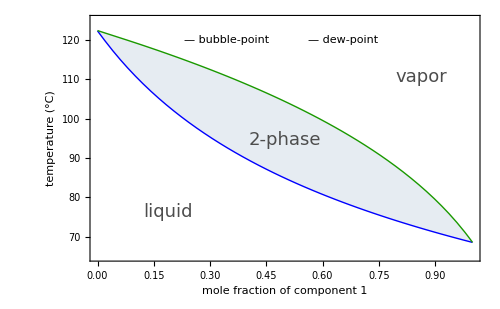
-Graphics-
Figure 13

```mathematica
Framed@Column[{Framed@Module[{Pe,Psat1e,Psat2e,i,Txtable,Tytable,Txx,Tyy},
Pe=0.7;
Psat1e[Te_]=0.00133322368*10^(6.90565-1211.033/(Te+220.79)); 
Psat2e[Te_]=0.00133322368*10^(6.65464-1344.8/(Te+219.48));  
i=0;
While[i<101,{xe=0.01*i,
s=FindRoot[xe*Psat1e[Te]+(1-xe)*Psat2e[Te]==Pe,{Te,40,190}];
xeq[i]=xe,
yeq[i]=(Psat1e[Te]*xe)/Pe/.s,
Teq[i]=Te/.s,i++}];
Txtable=Table[{xeq[i],Teq[i]},{i,1,100}];
Tytable=Table[{yeq[i],Teq[i]},{i,1,100}];
Txx=Interpolation[Txtable,InterpolationOrder->1];
Tyy=Interpolation[Tytable,InterpolationOrder->1];

Quiet@Plot[{Txx[x],Tyy[x]},{x,0,1},
PlotRange->{{0,1},{65,125}},ImageSize->500,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->{
Inset[Text@Style[Row[{Style["—",20,Blue]," bubble-point"}],16,FontFamily->"Arial"],Scaled[{0.35,0.9}]],
Inset[Text@Style[Row[{Style["—",20,RGBColor[0.1,0.6,0]]," dew-point"}],16,FontFamily->"Arial"],Scaled[{0.65,0.9}]],
Inset[Style["liquid",18,Darker[Gray,0.4],FontFamily->"Arial"],Scaled[{0.2,0.2}]],
Inset[Style["vapor",18,Darker[Gray,0.4],FontFamily->"Arial"],Scaled[{0.85,0.75}]],
Inset[Style["2-phase",18,Darker[Gray,0.4],FontFamily->"Arial"],{0.5,0.5*(Txx[0.5]+Tyy[0.5])}]
}]],Text@Style["Figure 13",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center]
```

For an ideal mixture at constant overall composition (z_1=0.5) use the simulations below to see how varying temperature affects the amount of liquid and vapor and the molar compositions of each phase.

As temperature increases, the mixture vaporizes (Figure 14).

```mathematica
Framed[Column[{Manipulate[Module[{Tx,Ty,x1,y1,leverL,leverV,p1,p2,p3},
Tx=Interpolation[{{0.05,116.17593775316534},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869732},{0.2,102.20948552122492},{0.25,98.57815974289365},{0.30000000000000004,95.30990723431995},{0.35000000000000003,92.34572393006421},{0.4,89.63921049336349},{0.45,87.15333748547953},{0.5,84.85815968745945},{0.55,82.72917092945056},{0.6000000000000001,80.74609966165225},{0.65,78.89201335805389},{0.7000000000000001,77.15264298968454},{0.75,75.51586677076592},{0.8,73.97131084335041},{0.8500000000000001,72.51003696546866},{0.9,71.12429573098638},{0.9500000000000001,69.80732971380557},{1.,68.55321505054492}}];
Ty=Interpolation[{{0.19520547470774982,116.17593775316534},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869732},{0.5459474339199167,102.20948552122492},{0.6186280724359985,98.57815974289365},{0.6782730999826126,95.30990723431995},{0.7279222867367744,92.34572393006421},{0.7697651621557392,89.63921049336349},{0.8054130860444707,87.15333748547953},{0.8360746698514914,84.85815968745945},{0.8626718897371343,82.72917092945056},{0.8859187711815474,80.74609966165225},{0.9063758492293178,78.89201335805389},{0.9244885885770282,77.15264298968454},{0.940614960755704,75.51586677076592},{0.9550455524788249,73.97131084335041},{0.9680184401823779,72.51003696546866},{0.9797303388255023,71.12429573098638},{0.9903450598913365,69.80732971380557},{1.0000000000000009,68.55321505054492}}];
x1=Quiet[x/.FindRoot[Tx[x]==t,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==t,{x,0.1}]];
leverL=Which[t≤Tx[0.5],1,Tx[0.5]<t<Ty[0.5],(y1-0.5)/(y1-x1),t≥Ty[0.5],0];
leverV=1-leverL;
p1=Quiet@Plot[{Tx[x],Ty[x]},{x,0,1},
PlotRange->{{0,1},{65,125}},ImageSize->{450,300},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,t}]];
p2=BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[
If[leverL==1∨leverV==1,Text@"",
{{Thick,Dashed,Blue,Line[{{x1,t},{0.5,t}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,t},{y1,t}}]}}]
];
Row[{Show[p1,p3],Show[p2]}]
],{{t,94.6,"temperature (°C)"},75,115,5,Appearance->"Labeled"}],
Text@Style["Figure 14",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 14

The screencast T-x-y Diagram: Lever Rule (Review) discusses the lever rule and T-x-y diagrams.

### Effect on Molar Composition in the Liquid and Vapor Phases

Test Yourself

A 50/50 mol% mixture of A and B is heated at constant pressure. What happens to the liquid (x_A) and vapor (y_A) mole fractions as temperature  increases (Figure 15)?

Hint

Recall what happens to x_A and y_A as pressure is increased.

A. x_A increases, y_A increases

Incorrect.

B. x_A increases, y_A decreases

Incorrect.

C. x_A decreases, y_A increases

Incorrect.

D. x_A decreases, y_A decreases

Correct. Use the slider in Figure 16 to increase the temperature.

```mathematica
Framed[Column[{Manipulate[Module[{Tx,Ty,x0,y0,x1,y1,leverL,leverV,p1,p2},
Tx=Interpolation[{{0.05,116.17593775316534},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869732},{0.2,102.20948552122492},{0.25,98.57815974289365},{0.30000000000000004,95.30990723431995},{0.35000000000000003,92.34572393006421},{0.4,89.63921049336349},{0.45,87.15333748547953},{0.5,84.85815968745945},{0.55,82.72917092945056},{0.6000000000000001,80.74609966165225},{0.65,78.89201335805389},{0.7000000000000001,77.15264298968454},{0.75,75.51586677076592},{0.8,73.97131084335041},{0.8500000000000001,72.51003696546866},{0.9,71.12429573098638},{0.9500000000000001,69.80732971380557},{1.,68.55321505054492}}];
Ty=Interpolation[{{0.19520547470774982,116.17593775316534},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869732},{0.5459474339199167,102.20948552122492},{0.6186280724359985,98.57815974289365},{0.6782730999826126,95.30990723431995},{0.7279222867367744,92.34572393006421},{0.7697651621557392,89.63921049336349},{0.8054130860444707,87.15333748547953},{0.8360746698514914,84.85815968745945},{0.8626718897371343,82.72917092945056},{0.8859187711815474,80.74609966165225},{0.9063758492293178,78.89201335805389},{0.9244885885770282,77.15264298968454},{0.940614960755704,75.51586677076592},{0.9550455524788249,73.97131084335041},{0.9680184401823779,72.51003696546866},{0.9797303388255023,71.12429573098638},{0.9903450598913365,69.80732971380557},{1.0000000000000009,68.55321505054492}}];
x0=0.305011;
y0=0.683658;
x1=Quiet[x/.FindRoot[Tx[x]==t,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==t,{x,0.1}]];
leverL=Which[t≤Tx[0.5],1,Tx[0.5]<t<Ty[0.5],(y1-0.5)/(y1-x1),t≥Ty[0.5],0];
leverV=1-leverL;
p1=Quiet@Plot[{Tx[x],Ty[x]},{x,0,1},
PlotRange->{{0,1},{65,125}},ImageSize->400,Frame->True,FrameLabel->{Style["mole fraction of component A",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}}];
p2=Graphics[{
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,65},{x0,95},{0.5,95}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{0.5,95},{y0,95},{y0,0.65}}]},
{Gray,PointSize[0.02],Point[{0.5,95}]},
{Thick,Dashed,Blue,Line[{{x1,65},{x1,t},{0.5,t}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,t},{y1,t},{y1,65}}]},
{PointSize[0.02],Point[{0.5,t}]},
If[t==95,Text@"",{{Thick,Arrow[{{x0,70},{x1,70}}]},{Thick,Arrow[{{y0,70},{y1,70}}]}}]
}];
Show[p1,p2]
],{{t,95,"temperature (°C)"},85,104,1,Appearance->"Labeled"}],
Text@Style["Figure 16",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 16

```mathematica
Framed@Column[{
Framed@Graphics3D[{
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,2}},0.75]},
{Gray,Cylinder[{{0,0,1.65},{0,0,1.85}},0.75]},
{RGBColor[0.,0.65,0.9],Cylinder[{{0,0,0},{0,0,0.55}},0.75]},
{FaceForm[Black],Cuboid[{-0.25,0,1.85},{0.25,0,2.25}]},
Text[Style[Column[{"vapor","y_A = 0.68"},Alignment->Center],18,FontFamily->"Arial"],{0,0,1.}],
Text[Style[Column[{"liquid","x_A = 0.31"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},Background->White,ImageSize->150],
Text@Style["Figure 15",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]
```

-Graphics3D-
Figure 15

The screencast: Phase Equilibrium: T-x-y Diagram presents more details on this type question.

### Adding Energy to a System

As heat is added to the system, the temperature increases and the solution vaporizes once the bubble point is reached. In Figure 17, a 50/50 mixture is in vapor-liquid equilibrium at constant pressure. Use the play button to add heat to the system and observe how the amounts of liquid and vapor change. Is the rate of temperature increaes the same in the three regions on the phase diagram if heat is added at a constant rate?

```mathematica
Framed[Column[{Quiet@Manipulate[Module[{Tx,Ty,x1,y1,leverL,leverV,T,p1,p2,p3,p4},
Tx=Interpolation[{{0.05,116.17593775316534},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869732},{0.2,102.20948552122492},{0.25,98.57815974289365},{0.30000000000000004,95.30990723431995},{0.35000000000000003,92.34572393006421},{0.4,89.63921049336349},{0.45,87.15333748547953},{0.5,84.85815968745945},{0.55,82.72917092945056},{0.6000000000000001,80.74609966165225},{0.65,78.89201335805389},{0.7000000000000001,77.15264298968454},{0.75,75.51586677076592},{0.8,73.97131084335041},{0.8500000000000001,72.51003696546866},{0.9,71.12429573098638},{0.9500000000000001,69.80732971380557},{1.,68.55321505054492}}];
Ty=Interpolation[{{0.19520547470774982,116.17593775316534},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869732},{0.5459474339199167,102.20948552122492},{0.6186280724359985,98.57815974289365},{0.6782730999826126,95.30990723431995},{0.7279222867367744,92.34572393006421},{0.7697651621557392,89.63921049336349},{0.8054130860444707,87.15333748547953},{0.8360746698514914,84.85815968745945},{0.8626718897371343,82.72917092945056},{0.8859187711815474,80.74609966165225},{0.9063758492293178,78.89201335805389},{0.9244885885770282,77.15264298968454},{0.940614960755704,75.51586677076592},{0.9550455524788249,73.97131084335041},{0.9680184401823779,72.51003696546866},{0.9797303388255023,71.12429573098638},{0.9903450598913365,69.80732971380557},{1.0000000000000009,68.55321505054492}}];

T=If[Q1<84.86,Q1,If[Q2<104.3,Q2,Q3]];

x1=Quiet[x/.FindRoot[Tx[x]==T,{x,0.1}]];
y1=Quiet[x/.FindRoot[Ty[x]==T,{x,0.1}]];
leverL=Which[T≥Ty[0.5],0,Tx[0.5]<T<Ty[0.5],(y1-0.5)/(y1-x1),T≤Tx[0.5],1];
leverV=1-leverL;

p1=Quiet@Plot[{Tx[x],Ty[x]},{x,0,1},PlotRange->{{0,1},{65,125}},ImageSize->{450,300},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,T}]];
p2=BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},PlotRange->{0,1}];
p3=Graphics[If[Tx[0.5]<T<Ty[0.5],
{{Thick,Dashed,Blue,Line[{{x1,T},{0.5,T}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,T},{y1,T}}]}},Text@""]];
p4=Graphics[{
Text[If[leverL==0,"",Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White]],{1,0.5*leverL}],
Text[If[leverV==0,"",Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]],{1,1-0.5*leverV}]
}];
Row[{Show[p1,p3],Show[p2,p4]}]
],
Row[{
Control[{{Q1,75,"add heat"},75,86,Trigger,AnimationRate->5,AppearanceElements->"PlayPauseButton"}],Button["reset",{Q1=75,Q2=81.07,Q3=22.93},ImageSize->Small],
Control[{{Q2,81.07,""},81.07,105,Trigger,AppearanceElements->None,AnimationRate->2,AnimationRunning->If[Q1==75,False,True]}],
Control[{{Q3,22.93,""},22.93,120,Trigger,AppearanceElements->None,AnimationRate->7,AnimationRunning->If[Q1==75,False,True]}]
}]
],
Text@Style["Figure 17",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 17

## Changes in Pressure

Test Yourself

What  happen if pressure is increased at constant temperature and constant overall composition?

A. Vaporize

Incorrect.

B. Condense

Correct. As pressure increases, the mixture is compressed and condenses.

Use the buttons below to change the pressure of the system (Figure 18).

```mathematica
Framed[Column[{Manipulate[Module[{Tx07,Ty07,Tx1,Ty1,Tx12,Ty12,x1,y1,leverL,leverV,cg,p1,p2,p3,g,pL},
Tx07=Quiet@Interpolation[{{0.05,116.1759377531654},{0.1,110.89064288898308},{0.15000000000000002,106.28016426869735},{0.2,102.20948552124158},{0.25,98.57815974291731},{0.30000000000000004,95.30990723434186},{0.35000000000000003,92.34572393007925},{0.4,89.63921049337175},{0.45,87.15333748548329},{0.5,84.85815968746093},{0.55,82.72917092945106},{0.6000000000000001,80.74609966162907},{0.65,78.89201335804907},{0.7000000000000001,77.15264298968357},{0.75,75.51586677076571},{0.8,73.97131084335035},{0.8500000000000001,72.51003696546861},{0.9,71.1242957309864},{0.9500000000000001,69.80732971380566},{1.,68.55321505054498}}];
Ty07=Quiet@Interpolation[{{0.19520547470775004,116.1759377531654},{0.3421787686820334,110.89064288898308},{0.4559066075854116,106.28016426869735},{0.5459474339201595,102.20948552124158},{0.6186280724363996,98.57815974291731},{0.6782730999830268,95.30990723434186},{0.7279222867370856,92.34572393007925},{0.7697651621559227,89.63921049337175},{0.8054130860445605,87.15333748548329},{0.8360746698515282,84.85815968746093},{0.8626718897371475,82.72917092945106},{0.8859187711809169,80.74609966162907},{0.9063758492291806,78.89201335804907},{0.9244885885769999,77.15264298968357},{0.9406149607556982,75.51586677076571},{0.9550455524788211,73.97131084335035},{0.9680184401823779,72.51003696546861},{0.9797303388255023,71.1242957309864},{0.9903450598913405,69.80732971380566},{1.0000000000000009,68.55321505054498}}];
Tx1=Quiet@Interpolation[{{0.05,129.9684312134107},{0.1,124.46728109026502},{0.15000000000000002,119.64739419823651},{0.2,115.37669169421264},{0.25,111.5558698415014},{0.30000000000000004,108.10883860676323},{0.35000000000000003,104.97628919904072},{0.4,102.11127586249542},{0.45,99.47612041144522},{0.5,97.04020282193841},{0.55,94.77835682830099},{0.6000000000000001,92.6696861586251},{0.65,90.69667822445331},{0.7000000000000001,88.8445314975093},{0.75,87.10063866222818},{0.8,85.45418488169182},{0.8500000000000001,83.89583220869729},{0.9,82.4174692238443},{0.9500000000000001,81.01201060130533},{1.,79.67323528381488}}];
Ty1=Quiet@Interpolation[{{0.1891953088265609,129.9684312134107},{0.3333713112040971,124.46728109026502},{0.4460245826904114,119.64739419823651},{0.5359266393575272,115.37669169421264},{0.6089748984048624,111.5558698415014},{0.6692536267616388,108.10883860676323},{0.7196657343789239,104.97628919904072},{0.7623221058077295,102.11127586249542},{0.7987889783092752,99.47612041144522},{0.8302494920928599,97.04020282193841},{0.8576118178980832,94.77835682830099},{0.8815831481153008,92.6696861586251},{0.9027213509478275,90.69667822445331},{0.9214716901180483,88.8445314975093},{0.9381933616570834,87.10063866222818},{0.9531789621472018,85.45418488169182},{0.9666689691862668,83.89583220869729},{0.9788626489648702,82.4174692238443},{0.9899263687136928,81.01201060130533},{0.9999999999999064,79.67323528381488}}];
Tx12=Quiet@Interpolation[{{0.05,137.46188498182605},{0.1,131.84143528370112},{0.15000000000000002,126.90618817074225},{0.2,122.525447073767},{0.25,118.60042515647964},{0.30000000000000004,115.05508518253845},{0.35000000000000003,111.82992921680345},{0.4,108.877704153133},{0.45,106.16037516935783},{0.5,103.64695434270998},{0.55,101.31191669241778},{0.6000000000000001,99.13402681521983},{0.65,97.09545723812461},{0.7000000000000001,95.18111721731337},{0.75,93.37813552342902},{0.8,91.67545740122351},{0.8500000000000001,90.06352722978299},{0.9,88.53403625013101},{0.9500000000000001,87.07972022300791},{1.,85.69419578304576}}];
Ty12=Quiet@Interpolation[{{0.18618575239455035,137.46188498182605},{0.32892560866402437,131.84143528370112},{0.44100386058226426,126.90618817074225},{0.5308079508250124,122.525447073767},{0.6040217842526161,118.60042515647964},{0.6646080724511306,115.05508518253845},{0.7153993423594157,111.82992921680345},{0.7584653435155831,108.877704153133},{0.7953482674507051,106.16037516935783},{0.827217369191567,103.64695434270998},{0.8549730525583759,101.31191669241778},{0.8793184552939417,99.13402681521983},{0.9008096469883358,97.09545723812461},{0.9198914554710375,95.18111721731337},{0.9369234500070746,93.37813552342902},{0.9521990642491066,91.67545740122351},{0.9659598608268867,90.06352722978299},{0.9784063043248772,88.53403625013101},{0.9897059906466085,87.07972022300791},{0.9999999999999993,85.69419578304576}}];
x1=Quiet[x/.FindRoot[Which[CG==1,Tx07[x],CG==2,Tx1[x],CG==3,Tx12[x]]==105,{x,0.1}]];
y1=Quiet[x/.FindRoot[Which[CG==1,Ty07[x],CG==2,Ty1[x],CG==3,Ty12[x]]==105,{x,0.2}]];
leverL=If[CG==1,0,(y1-0.5)/(y1-x1)];
leverV=1-leverL;
cg=Sequence[PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["temperature (°C)",16]},LabelStyle->{Black,FontFamily->"Arial"},PlotRange->{{0,1},{65,150}},ImageSize->{450,300},Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,105}]];
p1=Quiet@Plot[{Tx07[x],Ty07[x]},{x,0,1},Evaluate@cg];
p2=Quiet@Plot[{Tx1[x],Ty1[x]},{x,0,1},Evaluate@cg];
p3=Quiet@Plot[{Tx12[x],Ty12[x]},{x,0,1},Evaluate@cg];
g=Graphics[If[Which[CG==1,Ty07[0.5],CG==2,Ty1[0.5],CG==3,Ty12[0.5]]≤105,Text@"",
{{Thick,Dashed,Blue,Line[{{x1,105},{0.5,105}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,105},{y1,105}}]}}]];
pL=BarChart[{leverL,leverV},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverL,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*leverV,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
Switch[CG,1,Row[{Show[p1,g],Show[pL]}],2,Row[{Show[p2,g],Show[pL]}],3,Row[{Show[p3,g],Show[pL]}]]],
{{CG,2,"pressure (bar)"},{1->"0.7",2->"1.0",3->"1.2"},SetterBar}],Text@Style["Figure 18",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 18